## From Lab Frame

```mathematica
(* Lab Frame *)
E1, m1,p1,E2, m2, p2=0
(* Other Frame *)
```

```mathematica
(* Lorentz Transform *)
L=1/(√(1-β^2))({{1, β}, {β, 1}});
```

```mathematica
(* Lab frame relation *)
E1^2==p1^2 c^2+m1^2 c^4
E2==m2 c^2
```

```mathematica
(* Other Frame relation *)
Ec1^2==pc1^2 c^2+m1^2 c^4
Ec2^2==pc2^2 c^2+m2^2 c^4
```

```mathematica
(* They are connetted by the Lorentz Transform *)
L.{E1,p1 c}=={Ec1,pc1 c}
L.{m2 c^2,0}=={Ec2,pc2 c}
```

{E1/(√(1-β^2))+(c p1 β)/(√(1-β^2)),(c p1)/(√(1-β^2))+(E1 β)/(√(1-β^2))}=={Ec1,c pc1}

{(c^2 m2)/(√(1-β^2)),(c^2 m2 β)/(√(1-β^2))}=={Ec2,c pc2}

```mathematica
(* 4 equations 4 unknown *)
E1/(√(1-β^2))+(c p1 β)/(√(1-β^2))==Ec1,p1/(√(1-β^2))+(E1 β/c)/(√(1-β^2))==pc1,
(c^2 m2)/(√(1-β^2))==Ec2,(c m2 β)/(√(1-β^2))==pc2
```

```mathematica
(E1/(√(1-β^2))+(p1 β)/(√(1-β^2))+(c^2 m2)/(√(1-β^2)))/(E1+c^2 m2)/.p1->√(E1^2-m1^2 c^4)/. E1->α m1 c^2/. m2->1/.m1->m//Simplify
```

(c^2 (1+m α)+√(c^4 m^2 (-1+α^2)) β)/(c^2 (1+m α) √(1-β^2))

```mathematica
Solve[α == 1/(√(1-β^2)),β]
```

{{β→-√(1-1/α^2)},{β→√(1-1/α^2)}}

```mathematica
Manipulate[
Plot[{(1+1 m α+√(m^2 (-1+α^2)) β)/((1+ m α) √(1-β^2)),√(1-1/α^2)},{α,1,10},PlotRange->{{1,9},{0,2}}],{{m,1},0.1,4},{{β,0},-1,1}]
```

```mathematica
(* Solve pc1 == pc2 *)
Solve[p1/(√(1-β^2))+(E1 β/c)/(√(1-β^2))==(c m2 β)/(√(1-β^2)),β]
```

{{β→-p1/(E1-m2)}}

```mathematica
(* Ec1 *)
E1/(√(1-β^2))+(c p1 β)/(√(1-β^2))/.p1-> √(E1-m1) √(E1+m1)//FullSimplify
```

(E1+√(E1-m1) √(E1+m1) β)/(√(1-β^2))

```mathematica
(E1+√(E1-m1) √(E1+m1) β)/(√(1-β^2))/.β->(-√(E1-m1) √(E1+m1))/(-E1+c^2 m2) //FullSimplify
```

(E1+((E1-m1) (E1+m1))/(E1-m2))/(√((m1^2+m2 (-2 E1+m2))/(E1-m2)^2))

```mathematica
(E1+((E1-m1) (E1+m1))/(E1-m2))/(√((m1^2+m2 (-2 E1+m2))/(E1-m2)^2))/.{m1->m,m2->m}//Simplify
```

(2 E1+m)/(√2 √(-m/(E1-m)))

```mathematica
(2 E1+m)/(√2 √(-m/(E1-m)))/.E1-> α m c^2//Simplify
```

(m+2 m α)/(√2 √(1/(1-α)))

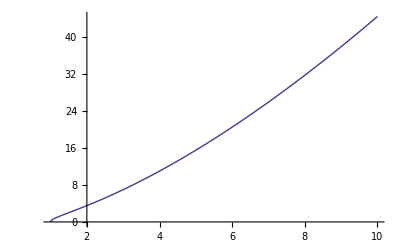

```mathematica
Plot[(1+2  α)/(√2 √(1/(α-1))),{α,0,10}, PlotRange->All]
```

## From CM frame

```mathematica
(* momentum 4 vector *)
P1i={√(p^2+m1^2),p ,0};
P2i={√(p^2+m2^2),-p ,0};
P1f={√(p^2+m1^2),p Cos[θ] ,p Sin[θ] };
P2f={√(p^2+m2^2),-p Cos[θ] ,-p Sin[θ] };
```

```mathematica
P1i+P2i == P1f+P2f
```

{√(m1^2+p^2)+√(m2^2+p^2),0,0}=={√(m1^2+pf^2)+√(m2^2+pf^2),0,0}

```mathematica
Solve[√(m1^2+p^2)+√(m2^2+p^2)==√(m1^2+pf^2)+√(m2^2+pf^2),pf]
```

{{pf→-p},{pf→p}}

```mathematica
(* Lorentz Transform *)
L =1/(√(1-β^2)){{1,β,0},{β,1,0},{0,0,1}};
%//MatrixForm
```

(1/(√(1-β^2)) | β/(√(1-β^2)) | 0
β/(√(1-β^2)) | 1/(√(1-β^2)) | 0
0 | 0 | 1/(√(1-β^2)))

```mathematica
L.P2i
```

{(√(m2^2+p^2))/(√(1-β^2))-(p β)/(√(1-β^2)),-p/(√(1-β^2))+(√(m2^2+p^2) β)/(√(1-β^2)),0}

```mathematica
Solve[-p/(√(1-β^2))+(√(m2^2+p^2) β)/(√(1-β^2))==0,β]
```

{{β→p/(√(m2^2+p^2))}}

```mathematica
(* Therefore, the Lorentz tranform of β = E2i/p can transfer to lab frame that particle 2 is stationary *)
```

```mathematica
Lrest=1/(√(1-(p/(√(m2^2+p^2)))^2)){{1,p/(√(m2^2+p^2)),0},{p/(√(m2^2+p^2)),1,0},{0,0,1}}//Simplify;
%//MatrixForm
```

(1/(√(m2^2/(m2^2+p^2))) | p/(√(m2^2/(m2^2+p^2)) √(m2^2+p^2)) | 0
p/(√(m2^2/(m2^2+p^2)) √(m2^2+p^2)) | 1/(√(m2^2/(m2^2+p^2))) | 0
0 | 0 | 1/(√(m2^2/(m2^2+p^2))))

```mathematica
P1ilab=Refine[Lrest.P1i//Simplify,{m2^2+p^2>0,m2>0}]
P2ilab=Refine[Lrest.P2i//Simplify,{m2^2+p^2>0,m2>0}]
```

{(p^2+√(m1^2+p^2) √(m2^2+p^2))/m2,(p (√(m1^2+p^2)+√(m2^2+p^2)))/m2,0}

{m2,0,0}

```mathematica
Energyratio=(√(p^2+m1^2)+√(p^2+m2^2))/((p^2+√(m1^2+p^2) √(m2^2+p^2))/m2+m2)//Simplify
```

(m2 (√(m1^2+p^2)+√(m2^2+p^2)))/(m2^2+p^2+√(m1^2+p^2) √(m2^2+p^2))

```mathematica
P1flab=Refine[Lrest.P1f//Simplify,{m2^2+p^2>0,m2>0}]
P2flab=Refine[Lrest.P2f//Simplify,{m2^2+p^2>0,m2>0}]
```

{(√(m1^2+p^2) √(m2^2+p^2)+p^2 Cos[θ])/m2,(p (√(m1^2+p^2)+√(m2^2+p^2) Cos[θ]))/m2,(p √(m2^2+p^2) Sin[θ])/m2}

{(m2^2+p^2-p^2 Cos[θ])/m2,(√(m2^2+p^2) (p-p Cos[θ]))/m2,-(p √(m2^2+p^2) Sin[θ])/m2}

```mathematica
(P1flab-P1ilab)//Simplify
```

{(p^2 (-1+Cos[θ]))/(√(m2^2/(m2^2+p^2)) √(m2^2+p^2)),(p (-1+Cos[θ]))/(√(m2^2/(m2^2+p^2))),(p Sin[θ])/(√(m2^2/(m2^2+p^2)))}

```mathematica
(* new angle of P1 *)
θ1lab[m1_,m2_,p_,θ_]:=ArcTan[ Sin[θ °]/((√(m1^2+p^2)+√(m2^2+p^2) Cos[θ °])/(√(m2^2+p^2))) ] 180/π;
θ2lab[m1_,m2_,p_,θ_]:=ArcTan[ -Sin[θ °]/(1-Cos[θ °])] 180/π;
```

```mathematica
Manipulate[
Plot[{θ1lab[m1,1,p,θ],θ2lab[m1,1,p,θ],θ, (θ1lab[m1,1,p,θ]+θ2lab[m1,1,p,θ])},{θ,0,180},PlotRange->{-180,180},AspectRatio->2], {p,0,10},{m1,0.1,4}]
```